```mathematica
<<NetLogo`
$NLHome="/home/erikasv/Downloads/netlogo-4.0.5/";
NLStart[];
NLCommand["no-display"];
NLLoadModel[ToFileName[{$NLHome,"test"},"modelo.nlogo"]];
```

```mathematica
Experiment1[p_]:=Module[{},
NLCommand["set num-people ",p,"setup"];
Mean[NLDoReport["go","clustering-coefficient",100]]
];
people=Table[i,{i,10,1000,10}];
NLCommand["no-display"];
clusteringData=Map[Experiment1,people];
```

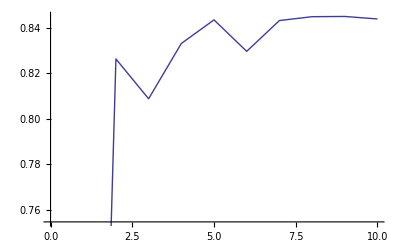

```mathematica
ListPlot[clusteringData,Joined->True]
```

```mathematica
Experiment2[p_]:=Module[{},
NLCommand["set num-people ",p, "set reduce-documents? True", "set vote-threshold 3","setup"];
Mean[NLDoReport["go","clustering-coefficient",10]]
];
```

```mathematica
people=Table[i,{i,10,10000,10}];
NLCommand["no-display"];
clusteringData1=Map[Experiment2,people];
```

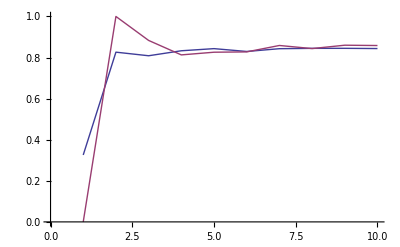

```mathematica
ListPlot[{clusteringData,clusteringData1},Joined->True,PlotRange->{{0,10},{0.,1}}]
```

```mathematica
hola
```

hola